## Equations

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

SetOptions[ContractMetric,AllowUpperDerivatives->True];
```

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l}]

DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD->{"|","∇"},FlatMetric->True,PrintAs->"g"];

SetOptions[ContractMetric,AllowUpperDerivatives->True];

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensor[PhiC[],M4,PrintAs->"φ^*"]

DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[d][Phi[]]CD[-d][PhiC[]]]]
```

(∇_d φ^* ∇^d φ)

```mathematica
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[α]
```

```mathematica
DefTensor[n[a],M4]
DefTensor[nc[a],M4]
DefTensor[n2[a,b],M4]
DefTensor[nc2[a,b],M4]

Rulescalartovector=MakeRule[{CD[b][Phi[]],n[b]}]
Rulescalartovector2=MakeRule[{CD[b][PhiC[]],nc[b]}]

Rulevectosca=MakeRule[{n[b],CD[b][Phi[]]}]
Rulevectosca2=MakeRule[{nc[b],CD[b][PhiC[]]}]

Rule3=MakeRule[{CD[a][n[b]],n2[a,b]}]
Rule3inv=MakeRule[{n2[a,b],CD[a][n[b]]}]

Rule4=MakeRule[{CD[a][nc[b]],nc2[a,b]}]
Rule4inv=MakeRule[{nc2[a,b],CD[a][nc[b]]}]

ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detmetric[]->-1};
rule:={Rulevectosca,Rulevectosca2,Rule3inv, Rule4inv, ruleflat}
```

{HoldPattern[∇^UnderBar[b̲] φ]:>Module[{},n | b
 ]}

{HoldPattern[∇^UnderBar[b̲] φ^*]:>Module[{},nc | b
 ]}

{HoldPattern[n | UnderBar[b̲]
 ]:>Module[{},∇^b φ]}

{HoldPattern[nc | UnderBar[b̲]
 ]:>Module[{},∇^b φ^*]}

{HoldPattern[∇^UnderBar[a̲] n | UnderBar[b̲]
 ]:>Module[{},n2 | a | b
  |  ]}

{HoldPattern[n2 | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{},∇^a n | b
 ]}

{HoldPattern[∇^UnderBar[a̲] nc | UnderBar[b̲]
 ]:>Module[{},nc2 | a | b
  |  ]}

{HoldPattern[nc2 | UnderBar[a̲] | UnderBar[b̲]
  |  ]:>Module[{},∇^a nc | b
 ]}

### Test

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
Ltry=Sqrt[-Detmetric[]]( -X[]-mS^2 Phi[]PhiC[])//NoScalar
LtryC=(Ltry//NoScalar)/.Rulescalartovector/.Rulescalartovector2
```

√(-g^OverTilde[~]) (-m^2 φ φ^*-∇_a φ^* ∇^a φ)

√(-g^OverTilde[~]) (-n | a
  nc |  
a-m^2 φ φ^*)

j^μ=dL/(d(d_μ ϕ))δϕ

```mathematica
cj=VarD[n[i]][LtryC]deltaPhi+VarD[nc[i]][LtryC]deltaPhiC/.Rulevectosca/.Rulevectosca2/.ruleflat//ContractMetric//Simplification
```

-ⅈ θ (φ^* ∇_i φ-φ ∇_i φ^*)

### Horndeski

```mathematica
LH=Sqrt[-Detmetric[]]*(-mS^2*PhiC[]*Phi[]-X[]+2eta *X[]*(CD[-f]@CD[f]@PhiC[]*CD[-h]@CD[h]@Phi[]-CD[f]@CD[h]@PhiC[]*CD[-f]@CD[-h]@Phi[]));
LHC=(LH//NoScalar)/.Rulescalartovector/.Rulescalartovector2/.Rule3/.Rule4
```

√(-g^OverTilde[~]) (-n | a
  nc |  
a+2 η n | b
  nc |  
b (n2 |   | h
h |   nc2 |   | f
f |  -n2 |   |  
f | h nc2 | f | h
  |  )-m^2 φ φ^*)

```mathematica
(*current*)
```

j^μ=dL/(d(d_μ ϕ))δϕ+d_ν(dL/(d(d_μ d_ν ϕ))δϕ)-2d_ν(dL/(d(d_μ d_ν ϕ)))δϕ

```mathematica
deltaPhi=-ⅈ α Phi[];
deltaPhiC= ⅈ α PhiC[];
```

```mathematica
cj1H=VarD[n[a]][LHC]deltaPhi+VarD[nc[a]][LHC]deltaPhiC//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj2H=CD[b][(VarD[n2[a, b]][LHC]deltaPhi)]+CD[b][(VarD[nc2[a, b]][LHC]deltaPhiC)]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj3H=-2CD[b][VarD[n2[a, b]][LHC]]deltaPhi-2CD[b][VarD[nc2[a, b]][LHC]]deltaPhiC//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
```

```mathematica
jHDown=cj1H+cj2H+cj3H//Simplification//ContractMetric//Simplification;
jH2Down=Collect[(ContractMetric[SortCovDs[jHDown,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify),{α ,eta},Simplify]
```

α (ⅈ (-φ^* ∇_a φ+φ ∇_a φ^*)+2 ⅈ η (-φ^* ∇_b ∇_a φ ∇^b φ^* ∇_c ∇^c φ+φ^* ∇_a φ ∇_b ∇^b φ ∇_c ∇^c φ^*-∇_a φ ∇_b φ^* ∇^b φ ∇_c ∇^c φ^*+φ ∇_b ∇_a φ ∇^b φ^* ∇_c ∇^c φ^*+∇_b ∇_a φ^* ∇^b φ (-φ^* ∇_c ∇^c φ+φ ∇_c ∇^c φ^*)+∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ-∇_b φ^* ∇^b φ ∇_c ∇_a φ ∇^c φ^*+φ^* ∇^b φ^* ∇_c ∇_a φ ∇^c ∇_b φ-φ ∇^b φ^* ∇_c ∇_a φ^* ∇^c ∇_b φ+φ^* ∇^b φ ∇_c ∇_a φ ∇^c ∇_b φ^*-φ ∇^b φ ∇_c ∇_a φ^* ∇^c ∇_b φ^*-φ^* ∇_a φ ∇_c ∇_b φ ∇^c ∇^b φ^*+∇_a φ^* (∇_b φ^* ∇^b φ ∇_c ∇^c φ-φ ∇_b ∇^b φ ∇_c ∇^c φ^*+φ ∇_c ∇_b φ ∇^c ∇^b φ^*)))

```mathematica
(*energy*)
```

Θ_μ^ν=-(dL/(d(d_ν ϕ))-d_γ(dL/(d(d_γ d_ν ϕ))))d_μ ϕ-dL/(d(d_ν d_γ ϕ))d_γ d_μ ϕ+δ_μ^γ L

```mathematica
e11H=-VarD[n[a]][LHC]n[-b]-VarD[nc[a]][LHC]nc[-b]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//ContractMetric//Simplification;
e12H=CD[c][VarD[n2[c, a]][LHC]]n[-b]+CD[c][VarD[nc2[c, a]][LHC]]nc[-b]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//ContractMetric//Simplification//Simplify;
e2H=-VarD[n2[a, c]][LHC]n2[c,-b]-VarD[nc2[a, c]][LHC]nc2[c,-b]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//ContractMetric//Simplification//Simplify;
```

```mathematica
e3H=metric[-a,-b]LH//. ruleflat;
```

```mathematica
eDownPart=e11H+e12H+e2H//Simplification;
eDownPart2=(ContractMetric[SortCovDs[eDownPart,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify)/.ruleflat;
eDownF=eDownPart2+e3H
```

-2 η (∇_b ∇_a φ^* ∇_c φ^* ∇^c φ ∇_d ∇^d φ+∇_b ∇_a φ ∇_c φ^* ∇^c φ ∇_d ∇^d φ^*-∇_b φ ∇_c ∇_a φ^* ∇^c φ ∇_d ∇^d φ^*-∇_b φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇^d φ^*-∇_c φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_b φ-∇_c φ^* ∇^c φ ∇_d ∇_a φ ∇^d ∇_b φ^*+∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ+∇_b φ ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ^*+∇_b φ^* (-∇_c ∇_a φ^* ∇^c φ ∇_d ∇^d φ-∇_c ∇_a φ ∇^c φ^* ∇_d ∇^d φ+∇_d ∇_a φ (∇^c φ^* ∇^d ∇_c φ+∇^c φ ∇^d ∇_c φ^*)))+∇_a φ^* ∇_b φ (1-2 η ∇_c ∇^c φ ∇_d ∇^d φ^*+2 η ∇_d ∇_c φ ∇^d ∇^c φ^*)+∇_a φ ∇_b φ^* (1-2 η ∇_c ∇^c φ ∇_d ∇^d φ^*+2 η ∇_d ∇_c φ ∇^d ∇^c φ^*)+g |   |  
a | b (-m^2 φ φ^*-(∇_a φ^* ∇^a φ)+2 η (∇_a φ^* ∇^a φ) (-∇_f ∇_h φ ∇^f ∇^h φ^*+∇_f ∇^f φ^* ∇_h ∇^h φ))

### beyond Horndeski

```mathematica
LBH=Sqrt[-Detmetric[]]*(-mS^2*PhiC[]*Phi[]-X[]+2eta *X[]*(CD[-h]@CD[h]@PhiC[]*CD[-i]@CD[i]@Phi[]-CD[h]@CD[i]@PhiC[]*CD[-h]@CD[-i]@Phi[])-2eta*(epsilonmetric[h,i,c,-d]*epsilonmetric[e,f,g,d]*CD[-h][PhiC[]]*CD[-e][Phi[]]*CD[-i][CD[-f][PhiC[]]]*CD[-c][CD[-g][Phi[]]]));
LBHC=((LBH//NoScalar)//ContractMetric)/.Rulescalartovector/.Rulescalartovector2/.Rule3/.Rule4//Simplify
```

-√(-g^OverTilde[~]) (n | a
  nc |  
a-2 η n | b
  n2 |   | i
i |   nc |  
b nc2 |   | h
h |  +2 η n | b
  n2 |   |  
h | i nc |  
b nc2 | h | i
  |  -2 η n |  
e (n2 |   | h
c |   nc |  
h nc2 | e | c
  |  -n2 |   | i
c |   nc | e
  nc2 |   | c
i |  +n2 | e | i
  |   nc |  
h nc2 |   | h
i |  -n2 | e | h
  |   nc |  
h nc2 |   | i
i |  +n2 |   | c
c |   (-nc |  
h nc2 | e | h
  |  +nc | e
  nc2 |   | i
i |  ))+m^2 φ φ^*)

```mathematica
(*current*)
```

```mathematica
cj1BH=VarD[n[a]][LBHC]deltaPhi+VarD[nc[a]][LBHC]deltaPhiC//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj2BH=CD[b][(VarD[n2[a, b]][LBHC]deltaPhi)]+CD[b][(VarD[nc2[a, b]][LBHC]deltaPhiC)]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
cj3BH=-2CD[b][VarD[n2[a, b]][LBHC]]deltaPhi-2CD[b][VarD[nc2[a, b]][LBHC]]deltaPhiC//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//Simplification;
```

```mathematica
jBHDown=cj1BH+cj2BH+cj3BH//Simplification//ContractMetric//Simplification;
jBH2Down=Collect[(ContractMetric[SortCovDs[jBHDown,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify),{ α,eta},Simplify]
```

α (ⅈ (-φ^* ∇_a φ+φ ∇_a φ^*)+2 ⅈ η (2 ∇_a φ^* ∇_b φ^* ∇^b φ ∇_c ∇^c φ+3 φ^* ∇_a φ ∇_b ∇^b φ ∇_c ∇^c φ^*-2 φ ∇_a φ^* ∇_b ∇^b φ ∇_c ∇^c φ^*-φ ∇_a φ ∇_b ∇^b φ^* ∇_c ∇^c φ^*-∇_a φ ∇_b φ^* (∇^b φ^* ∇_c ∇^c φ+∇^b φ ∇_c ∇^c φ^*)+∇_b ∇_a φ^* (φ ∇^b φ^* ∇_c ∇^c φ+∇^b φ (-3 φ^* ∇_c ∇^c φ+3 φ ∇_c ∇^c φ^*))+∇_b φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c φ-2 ∇_b φ^* ∇^b φ ∇_c ∇_a φ ∇^c φ^*-∇_a φ^* ∇^b φ ∇_c ∇_b φ ∇^c φ^*+∇_a φ ∇^b φ^* ∇_c ∇_b φ ∇^c φ^*+∇_b ∇_a φ (∇^b φ^* (-φ^* ∇_c ∇^c φ+2 φ ∇_c ∇^c φ^*)+∇^b φ (-2 φ^* ∇_c ∇^c φ^*+∇_c φ^* ∇^c φ^*))-φ^* ∇^b φ^* ∇_c ∇_b φ ∇^c ∇_a φ+2 φ^* ∇^b φ ∇_c ∇_b φ^* ∇^c ∇_a φ-φ ∇^b φ^* ∇_c ∇_b φ^* ∇^c ∇_a φ+2 φ^* ∇^b φ^* ∇_c ∇_a φ ∇^c ∇_b φ+2 φ^* ∇^b φ ∇_c ∇_a φ^* ∇^c ∇_b φ-2 φ ∇^b φ^* ∇_c ∇_a φ^* ∇^c ∇_b φ+φ^* ∇^b φ ∇_c ∇_a φ ∇^c ∇_b φ^*-3 φ ∇^b φ ∇_c ∇_a φ^* ∇^c ∇_b φ^*-2 φ^* ∇_a φ ∇_c ∇_b φ^* ∇^c ∇^b φ+φ ∇_a φ^* ∇_c ∇_b φ^* ∇^c ∇^b φ-φ^* ∇_a φ ∇_c ∇_b φ ∇^c ∇^b φ^*+φ ∇_a φ^* ∇_c ∇_b φ ∇^c ∇^b φ^*+φ ∇_a φ ∇_c ∇_b φ^* ∇^c ∇^b φ^*))

```mathematica
(*energy*)
```

```mathematica
e11BH=-VarD[n[a]][LBHC]n[-b]-VarD[nc[a]][LBHC]nc[-b]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//ContractMetric//Simplification;
e12BH=CD[c][VarD[n2[c, a]][LBHC]]n[-b]+CD[c][VarD[nc2[c, a]][LBHC]]nc[-b]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//ContractMetric//Simplification//Simplify;
e2BH=-VarD[n2[a, c]][LBHC]n2[c,-b]-VarD[nc2[a, c]][LBHC]nc2[c,-b]//. ruleflat//.Rule3inv//. Rule4inv//.Rulevectosca//.Rulevectosca2//ContractMetric//Simplification//Simplify;
```

```mathematica
e3BH=metric[-a,-b]LBH//. ruleflat;
```

```mathematica
eDownBHPart=e11BH+e12BH+e2BH//Simplification;
eDownBHPart2=(ContractMetric[SortCovDs[eDownBHPart,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify)/.ruleflat;
eDownFBH=eDownBHPart2+e3BH
```

-2 η (-2 ∇_b φ ∇_c ∇_a φ^* ∇^c φ^* ∇_d ∇^d φ+2 ∇_b ∇_a φ ∇_c φ^* ∇^c φ ∇_d ∇^d φ^*-∇_b φ ∇_c ∇_a φ^* ∇^c φ ∇_d ∇^d φ^*-3 ∇_b φ ∇_c ∇_a φ ∇^c φ^* ∇_d ∇^d φ^*+∇_c ∇_a φ^* ∇^c φ ∇_d ∇_b φ ∇^d φ^*+∇_c ∇_a φ ∇^c φ ∇_d ∇_b φ^* ∇^d φ^*-∇_b ∇_a φ ∇^c φ ∇_d ∇_c φ^* ∇^d φ^*+∇_b ∇_a φ^* ∇^c φ (2 ∇_c φ^* ∇_d ∇^d φ-∇_d ∇_c φ ∇^d φ^*)+∇_b φ ∇^c φ^* ∇_d ∇_c φ^* ∇^d ∇_a φ-2 ∇_b φ ∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ^*-2 ∇_c φ^* ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_b φ-2 ∇_c φ^* ∇^c φ ∇_d ∇_a φ ∇^d ∇_b φ^*+3 ∇_b φ ∇^c φ^* ∇_d ∇_a φ^* ∇^d ∇_c φ+∇_b φ ∇^c φ^* ∇_d ∇_a φ ∇^d ∇_c φ^*+3 ∇_b φ ∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ^*-∇_b φ^* (2 ∇_c ∇_a φ^* ∇^c φ ∇_d ∇^d φ+∇_c ∇_a φ (3 ∇^c φ^* ∇_d ∇^d φ+∇^c φ ∇_d ∇^d φ^*)+∇^c φ ∇_d ∇_c φ^* ∇^d ∇_a φ-3 ∇^c φ^* ∇_d ∇_a φ ∇^d ∇_c φ-∇^c φ ∇_d ∇_a φ^* ∇^d ∇_c φ-3 ∇^c φ ∇_d ∇_a φ ∇^d ∇_c φ^*))+∇_a φ (2 η ∇^c φ^* (∇_c ∇_b φ^* ∇_d ∇^d φ+∇_c ∇_b φ ∇_d ∇^d φ^*-∇_d ∇_c φ^* ∇^d ∇_b φ-∇_d ∇_b φ^* ∇^d ∇_c φ)+∇_b φ^* (1-4 η ∇_c ∇^c φ ∇_d ∇^d φ^*+2 η ∇_d ∇_c φ^* ∇^d ∇^c φ+2 η ∇_d ∇_c φ ∇^d ∇^c φ^*))+∇_a φ^* (2 η ∇_b φ^* (-∇_c ∇^c φ ∇_d ∇^d φ+∇_d ∇_c φ ∇^d ∇^c φ)+∇_b φ (1-6 η ∇_c ∇^c φ ∇_d ∇^d φ^*+4 η ∇_d ∇_c φ^* ∇^d ∇^c φ+2 η ∇_d ∇_c φ ∇^d ∇^c φ^*))+g |   |  
a | b (-m^2 φ φ^*-(∇_a φ^* ∇^a φ)-2 η (g | e | i
  |   g | f | h
  |   g | g | c
  |  -g | e | h
  |   g | f | i
  |   g | g | c
  |  -g | e | i
  |   g | f | c
  |   g | g | h
  |  +g | e | c
  |   g | f | i
  |   g | g | h
  |  +g | e | h
  |   g | f | c
  |   g | g | i
  |  -g | e | c
  |   g | f | h
  |   g | g | i
  |  ) ∇_c ∇_g φ ∇_e φ ∇_h φ^* ∇_i ∇_f φ^*+2 η (∇_a φ^* ∇^a φ) (-∇_h ∇_i φ ∇^h ∇^i φ^*+∇_h ∇^h φ^* ∇_i ∇^i φ))

### Metric

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
MatrixForm[metricarray={{-1,0,0,0},{0,1,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
MetricInBasis[metric,-esf,metricarray]
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

{{g |   |  
0 | 0→-1,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→1,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

TensorValues::invalid: CDRiemannCD is not a valid expression for TensorValues.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];

(*ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];*)

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
(*ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];*)
```

```mathematica
jH=jH2Down//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify;
```

```mathematica
j0H=Collect[jH[[1]],{α,eta},Simplify]
```

α (2 w ϕ[r]^2-(4 η w (-r^2 ϕ'[r]^4+r ϕ[r] ϕ'[r]^2 (-2 ϕ'[r]+r ϕ''[r])+3 w^2 r ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+ϕ[r]^2 ϕ'[r] ((2+w^2 r^2) ϕ'[r]+4 r ϕ''[r])))/r^2)

```mathematica
Tener=eDownF//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify;
```

```mathematica
ener=Collect[Tener[[1,1]],{eta},Simplify]
```

(m^2+w^2) ϕ[r]^2+ϕ'[r]^2-(4 η (2 w^2 r^2 ϕ[r] ϕ'[r]^2 ϕ''[r]+2 w^4 r ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+w^2 ϕ[r]^2 ϕ'[r] (ϕ'[r]+2 r ϕ''[r])+ϕ'[r]^3 (ϕ'[r]+2 r ϕ''[r])))/r^2

```mathematica
jBH=jBH2Down//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify;
```

```mathematica
j0BH=Collect[jBH[[1]],{α,eta},Simplify]
```

α (2 w ϕ[r]^2-(4 η w (-r^2 ϕ'[r]^4+r ϕ[r] ϕ'[r]^2 (-6 ϕ'[r]+r ϕ''[r])+3 w^2 r ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+ϕ[r]^2 ϕ'[r] ((4+w^2 r^2) ϕ'[r]+8 r ϕ''[r])))/r^2)

```mathematica
TenerBH=eDownFBH//NoScalar//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify;
```

```mathematica
enerBH=Collect[TenerBH[[1,1]],{eta},Simplify]
```

(m^2+w^2) ϕ[r]^2+ϕ'[r]^2-(8 η (w^2 r ϕ[r] ϕ'[r]^2 (-ϕ'[r]+r ϕ''[r])+ϕ'[r]^3 (ϕ'[r]+r ϕ''[r])+w^4 r ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+w^2 ϕ[r]^2 ϕ'[r] (ϕ'[r]+2 r ϕ''[r])))/r^2

## Computing

```mathematica
Quit[]
```

```mathematica
j0H[r_?NumberQ]:=α (2 w ϕ[r]^2-(4 w η (-r^2 ϕ'[r]^4+r ϕ[r] ϕ'[r]^2 (-2 ϕ'[r]+r ϕ''[r])+3 r w^2 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+ϕ[r]^2 ϕ'[r] ((2+r^2 w^2) ϕ'[r]+4 r ϕ''[r])))/r^2);
 enerH[r_?NumberQ]:=(m^2+w^2) ϕ[r]^2+ϕ'[r]^2-(4 η (2 r^2 w^2 ϕ[r] ϕ'[r]^2 ϕ''[r]+2 r w^4 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+w^2 ϕ[r]^2 ϕ'[r] (ϕ'[r]+2 r ϕ''[r])+ϕ'[r]^3 (ϕ'[r]+2 r ϕ''[r])))/r^2;
```

```mathematica
j0BH[r_?NumberQ]:=α (2 w ϕ[r]^2-(4 w η (-r^2 ϕ'[r]^4+r ϕ[r] ϕ'[r]^2 (-6 ϕ'[r]+r ϕ''[r])+3 r w^2 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+ϕ[r]^2 ϕ'[r] ((4+r^2 w^2) ϕ'[r]+8 r ϕ''[r])))/r^2);
 enerBH[r_?NumberQ]:=(m^2+w^2) ϕ[r]^2+ϕ'[r]^2-(8 η (r w^2 ϕ[r] ϕ'[r]^2 (-ϕ'[r]+r ϕ''[r])+ϕ'[r]^3 (ϕ'[r]+r ϕ''[r])+r w^4 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+w^2 ϕ[r]^2 ϕ'[r] (ϕ'[r]+2 r ϕ''[r])))/r^2;
```

### Checking dimensionless

```mathematica
eqad=j0H/.{w-> ω mS, ϕ[r]-> σ/(mS^2 Sqrt[η]), ϕ'[r]-> dσ/(mS Sqrt[η]),ϕ''[r]->  ddσ/ Sqrt[η]}/.r-> x/mS//Simplify
eqSol=j0H/.{w-> ω , ϕ[r]-> σ, ϕ'[r]-> dσ,ϕ''[r]->  ddσ}/.r-> x/.{η-> 1, mS-> 1}//Simplify
Simplify[eqad*mS^3 η]-eqSol//Simplify
```

-(2 α ω (-2 dσ^4 x^2-4 dσ^3 x σ+4 dσ x σ^2 (2 ddσ+3 σ ω^2)+x^2 σ^2 (-1+6 ddσ σ ω^2)+2 dσ^2 σ (ddσ x^2+σ (2+x^2 ω^2))))/(mS^3 x^2 η)

2 α ω (σ^2-(2 (-dσ^4 x^2+dσ^2 x (-2 dσ+ddσ x) σ+3 x (2 dσ+ddσ x) σ^3 ω^2+dσ σ^2 (4 ddσ x+dσ (2+x^2 ω^2))))/x^2)

0

```mathematica
eqad=enerH/.{w-> ω mS, ϕ[r]-> σ/(mS^2 Sqrt[η]), ϕ'[r]-> dσ/(mS Sqrt[η]),ϕ''[r]->  ddσ/ Sqrt[η]}/.r-> x/mS//Simplify
eqSol=enerH/.{w-> ω , ϕ[r]-> σ, ϕ'[r]-> dσ,ϕ''[r]->  ddσ}/.r-> x/.{η-> 1, mS-> 1}//Simplify
Simplify[eqad*mS^2 η]-eqSol//Simplify
```

(-4 dσ^4-8 ddσ dσ^3 x-8 dσ x σ^2 ω^2 (ddσ+2 σ ω^2)+x^2 σ^2 (1+ω^2-8 ddσ σ ω^4)+dσ^2 (-4 σ^2 ω^2+x^2 (1-8 ddσ σ ω^2)))/(mS^2 x^2 η)

dσ^2+σ^2 (1+ω^2)-(4 (dσ^3 (dσ+2 ddσ x)+2 ddσ dσ^2 x^2 σ ω^2+dσ (dσ+2 ddσ x) σ^2 ω^2+2 x (2 dσ+ddσ x) σ^3 ω^4))/x^2

0

```mathematica
eqad=j0BH/.{w-> ω mS, ϕ[r]-> σ/(mS^2 Sqrt[η]), ϕ'[r]-> dσ/(mS Sqrt[η]),ϕ''[r]->  ddσ/ Sqrt[η]}/.r-> x/mS//Simplify
eqSol=j0BH/.{w-> ω , ϕ[r]-> σ, ϕ'[r]-> dσ,ϕ''[r]->  ddσ}/.r-> x/.{η-> 1, mS-> 1}//Simplify
Simplify[eqad*mS^3 η]-eqSol//Simplify
```

-(2 α ω (-2 dσ^4 x^2-12 dσ^3 x σ+4 dσ x σ^2 (4 ddσ+3 σ ω^2)+x^2 σ^2 (-1+6 ddσ σ ω^2)+2 dσ^2 σ (ddσ x^2+σ (4+x^2 ω^2))))/(mS^3 x^2 η)

2 α ω (σ^2-(2 (-dσ^4 x^2+dσ^2 x (-6 dσ+ddσ x) σ+3 x (2 dσ+ddσ x) σ^3 ω^2+dσ σ^2 (8 ddσ x+dσ (4+x^2 ω^2))))/x^2)

0

```mathematica
eqad=enerBH/.{w-> ω mS, ϕ[r]-> σ/(mS^2 Sqrt[η]), ϕ'[r]-> dσ/(mS Sqrt[η]),ϕ''[r]->  ddσ/ Sqrt[η]}/.r-> x/mS//Simplify
eqSol=enerBH/.{w-> ω , ϕ[r]-> σ, ϕ'[r]-> dσ,ϕ''[r]->  ddσ}/.r-> x/.{η-> 1, mS-> 1}//Simplify
Simplify[eqad*mS^2 η]-eqSol//Simplify
```

(-8 dσ^4-8 dσ^3 x (ddσ-σ ω^2)-16 dσ x σ^2 ω^2 (ddσ+σ ω^2)+x^2 σ^2 (1+ω^2-8 ddσ σ ω^4)+dσ^2 (-8 σ^2 ω^2+x^2 (1-8 ddσ σ ω^2)))/(mS^2 x^2 η)

dσ^2+σ^2 (1+ω^2)-(8 (dσ^3 (dσ+ddσ x)+dσ^2 x (-dσ+ddσ x) σ ω^2+dσ (dσ+2 ddσ x) σ^2 ω^2+x (2 dσ+ddσ x) σ^3 ω^4))/x^2

0

### Computing the Energy and Particle Number

E_0=∫Θ_0^0 √γ ⅆ^3 x,     N=∫j^0 √γ ⅆ^3 x

#### Horndeski

```mathematica
Quit[]
```

```mathematica
eqphi=-m^2 r^2 ϕ[r]+r α (r w^2 ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))==0;
```

```mathematica
seEq=(Series[eqphi[[1]],{r,0,8}]//Simplify)/.φ'[0]-> 0;
ord0=Coefficient[seEq,r,0];
ord1=Coefficient[seEq,r,1];
ord2=Coefficient[seEq,r,2];
ord3=Coefficient[seEq,r,3];
ord4=Coefficient[seEq,r,4];
ord5=Coefficient[seEq,r,5];
ord6=Coefficient[seEq,r,6];
ord7=Coefficient[seEq,r,7];
ord8=Coefficient[seEq,r,8];
```

```mathematica
eqPhi=Series[ϕ[r],{r,0,8}]/.φ'[0]-> 0//Normal;
eqdPhi=Series[ϕ'[r],{r,0,7}]/.φ'[0]-> 0//Normal;
```

```mathematica
(* one *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[1]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond1={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* two *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[2]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond2={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* three *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[3]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond3={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(*sigma=eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ;*)
```

```mathematica
ClearAll[w,mS,η,rMin,ϕ0]
```

```mathematica
SeidelEqsList={};
SeidelBCList1={};
SeidelBCList2={};
SeidelBCList3={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{eqphi}];
AppendTo[SeidelCoefFunctionsList,{φ}];

AppendTo[SeidelBCList1,cond1];
AppendTo[SeidelBCList2,cond2];
AppendTo[SeidelBCList3,cond3];

(*AppendTo[SeidelBCList,{φ[rMin]==ϕ0, φ'[rMin] == 0 }];*)
```

```mathematica
ini={SeidelBCList1, SeidelBCList2, SeidelBCList3};
```

```mathematica
datViableP={{0.67,0.99998046875,201.0000000005957,1}(*,{0.671,0.9999775303335917,201.00999999996216,1}*),{0.672,0.9999775303335917,201.00999999996216,1},{0.673,0.9999687150843667,201.00999999996216,1},{0.674,0.9999789995417958,201.00999999996216,1},{0.675,0.9999687150843667,201.00999999996216,1},{0.676,0.9999452077531001,201.00999999996216,1},{0.677,0.9999217004218335,201.00999999996216,1},{0.678,0.9998993352826282,142.99000000001493,1},{0.679,0.9998599936772586,201.00999999996216,1},{0.6795,0.9998464261591169,154.76000000000423,1},{0.7,0.9984759995489378,139.73100000030314,1},{0.72,0.9962075834622321,59.9839999999509,1},{0.74,0.9932927009293323,101.01000000011825,1},{0.76,0.9898964354584507,61.42399999994755,1},{0.78,0.9861317754171623,36.83300000000486,1},{0.8,0.9820802824199164,45.97499999998355,1},{0.82,0.9778025103732645,37.79500000000262,1},{0.84,0.9733433353477622,40.168999999997084,1},{0.86,0.9687350122072801,33.8110000000119,1},{0.88,0.9639970167958337,29.653000000013257,1},{0.9,0.9591309602305742,30.142000000013855,1},{0.92,0.95405,20,1}};
```

```mathematica
(*σ0, w, rMax, η*)
datViableN={{0.606,0.9999995207157898,201.0000000005957,-1},{0.63,0.9918107720880629,48.35399999997801,-1},{0.66,0.9773564575675739,53.314999999966446,-1},{0.67,0.9723871014804728,47.191999999980716,-1},{0.69,0.9624652220917436,54.62899999996338,-1},{0.7,0.9575473875684575,45.71899999998415,-1},{0.72,0.9478481489709842,26.170000000009,-1},{0.74,0.9383659516701663,33.16000000001342,-1},{0.76,0.9291239932949891,30.983000000014883,-1},{0.78,0.9201313108001683,30,-1},{0.8,0.9113897089244307,19.957000000001408,-1},{0.82,0.9028971062183845,21.124000000002834,-1},{0.84,0.8946481144672654,19.14000000000041,-1},{0.86,0.8866353439752958,18.500999999999628,-1},{0.88,0.878852101130706,28.34600000001166,-1},{0.9,0.8712895259625596,15.53399999999683,-1},{0.92,0.8639400693060306,18.179999999999236,-1},{0.94,0.8567948948772361,14.841999999997213,-1},{0.96,0.8498465804823888,16.706999999997436,-1},{0.98,0.8430871226575917,21.706000000003545,-1},{0.99,0.8397756686359639,17.550999999998467,-1},{1.,0.8365083431232883,17.74999999999871,-1},{1.2,0.7792281406244599,19.28900000000059,-1},{1.4,0.7338129340118398,20.05800000000153,-1},{1.6,0.696688024813614,13.304999999998065,-1},{1.8,0.6655979441170108,19.237000000000528,-1},{2.,0.6390553518425344,17.34199999999821,-1},{2.2,0.6160385486514806,14.640999999997325,-1},{2.4,0.5958204645637497,13.989999999997686,-1},{2.6,0.5778682884855366,10.475999999999633,-1},{2.8,0.5617811490863667,14.050999999997652,-1},{3.,0.5472513804946141,12.197999999998679,-1},{3.2,0.5340384133417744,13.159999999998146,-1},{3.4,0.5219506559272629,13.640999999997879,-1},{3.6,0.5108335204507295,11.065999999999306,-1},{3.8,0.5005611251183273,15.902999999996625,-1},{4.,0.4910292284122836,14.39799999999746,-1},{4.2,0.4821508284497754,10.745999999999484,-1},{4.4,0.4738526759966446,10.48199999999963,-1},{4.6,0.4660726898167017,17.55299999999847,-1},{4.8,0.45875779679090745,15.751999999996709,-1},{5.,0.4518622255255901,11.270999999999193,-1},{5.2,0.44534626650868525,11.481999999999076,-1},{5.4,0.4391754793410385,14.8649999999972,-1},{5.6,0.4333195263659412,14.1459999999976,-1},{5.8,0.42775183524014715,10.42599999999966,-1},{6,0.4224487319929132,10.894999999999401,-1},{6.2,0.41738942075742513,9.821999999999996,-1},{6.4,0.41255518759458343,12.625999999998442,-1},{6.6,0.4079293352782265,13.80099999999779,-1},{6.8,0.40349678011570467,15.359999999996926,-1},{7.,0.3992441870875326,12.622999999998443,-1},{7.2,0.3951591624249573,9.18400000000035,-1},{7.4,0.3912307662288609,12.91599999999828,-1},{7.6,0.38744884712284566,12.830999999998328,-1},{7.8,0.383804326062093,15.015999999997117,-1},{8.,0.38028867151359635,12.040999999998766,-1},{8.2,0.37689437454125085,12.197999999998679,-1},{8.4,0.37361427153800764,11.537999999999045,-1},{8.6,0.37044194713234824,9.889999999999958,-1},{8.8,0.3673713917031838,13.740999999997824,-1},{9,0.3643971614513011,14.799999999997237,-1},{9.2,0.3615140982921379,15.589999999996799,-1},{9.4,0.3587175201595687,11.735999999998935,-1},{9.6,0.35600301426608094,12.018999999998778,-1},{9.8,0.3533665013350388,14.039999999997658,-1},{10,0.3508041927445462,15.070999999997087,-1},{10.5,0.34470048721513374,12.435999999998547,-1},{11,0.33898990027055714,13.505999999997954,-1},{11.5,0.33363061831463847,14.526999999997388,-1},{12,0.3285868089031246,10.667999999999527,-1},{12.5,0.3238277198709476,13.715999999997837,-1},{13,0.31932661731185163,13.473999999997972,-1},{13.5,0.31506018683638926,15.639999999996771,-1},{14,0.3110080394430057,12.945999999998264,-1},{14.5,0.30715221231419754,12.21399999999867,-1},{15,0.3034767278946062,14.353999999997484,-1},{16,0.2966119177794746,11.759999999998922,-1},{17,0.2903176139688094,12.93499999999827,-1},{18,0.28451620983348436,15.037999999997105,-1},{19,0.2791444860990656,10.474999999999634,-1},{20,0.27414997514444917,10.295999999999733,-1},{25,0.2535202002185575,15.091999999997075,-1},{30,0.23790498835005225,15.385999999996912,-1},{35,0.22550549456370222,14.997999999997127,-1},{40,0.21532089827225892,16.621999999997332,-1},{45,0.20674252867311854,17.894999999998888,-1},{100,0.1572902583578016,17.81599999999879,-1},{200,0.12435372586010171,20.75300000000238,-1},{500,0.09134058144401483,25.52200000000821,-1},{600,0.08591815964638728,30,-1},{1000,0.07239699294378885,30.231000000013964,-1},{2000,0.0574112394001,43,-1}};
```

```mathematica
L1=1; η=1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.9591309602305742; rMax=30; α=1;(* .26,1.012476348812271000 *)
s1=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];
```

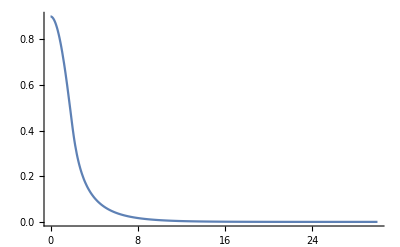

```mathematica
Plot[{Evaluate[φ[r]]/.s1},{r,rMin,rMax},PlotRange->All]
```

```mathematica
datViableN={{0.606,0.9999995207157898,201.0000000005957,-1},{0.63,0.9918107720880629,48.35399999997801,-1},{0.66,0.9773564575675739,53.314999999966446,-1},{0.67,0.9723871014804728,47.191999999980716,-1},{0.69,0.9624652220917436,45.62899999996338,-1},{0.7,0.9575473875684575,45.71899999998415,-1},{0.72,0.9478481489709842,26.170000000009,-1},{0.74,0.9383659516701663,33.16000000001342,-1},{0.76,0.9291239932949891,30.983000000014883,-1},{0.78,0.9201313108001683,30,-1},{0.8,0.9113897089244307,19.957000000001408,-1},{0.82,0.9028971062183845,21.124000000002834,-1},{0.84,0.8946481144672654,19.14000000000041,-1},{0.86,0.8866353439752958,18.500999999999628,-1},{0.88,0.878852101130706,28.34600000001166,-1},{0.9,0.8712895259625596,15.53399999999683,-1},{0.92,0.8639400693060306,18.179999999999236,-1},{0.94,0.8567948948772361,14.841999999997213,-1},{0.96,0.8498465804823888,16.706999999997436,-1},{0.98,0.8430871226575917,21.706000000003545,-1},{0.99,0.8397756686359639,17.550999999998467,-1},{1.,0.8365083431232883,17.74999999999871,-1},{1.2,0.7792281406244599,19.28900000000059,-1},{1.4,0.7338129340118398,20.05800000000153,-1},{1.6,0.696688024813614,13.304999999998065,-1},{1.8,0.6655979441170108,19.237000000000528,-1},{2.,0.6390553518425344,17.34199999999821,-1},{2.2,0.6160385486514806,14.640999999997325,-1},{2.4,0.5958204645637497,13.989999999997686,-1},{2.6,0.5778682884855366,10.475999999999633,-1},{2.8,0.5617811490863667,14.050999999997652,-1},{3.,0.5472513804946141,12.197999999998679,-1},{3.2,0.5340384133417744,10.159999999998146,-1},{3.4,0.5219506559272629,10.640999999997879,-1},{3.6,0.5108335204507295,11.065999999999306,-1},{3.8,0.5005611251183273,15.902999999996625,-1},{4.,0.4910292284122836,14.39799999999746,-1},{4.2,0.4821508284497754,10.745999999999484,-1},{4.4,0.4738526759966446,10.48199999999963,-1},{4.6,0.4660726898167017,10.55299999999847,-1},{4.8,0.45875779679090745,10.751999999996709,-1},{5.,0.4518622255255901,11.270999999999193,-1},{5.2,0.44534626650868525,11.481999999999076,-1},{5.4,0.4391754793410385,12.8649999999972,-1},{5.6,0.4333195263659412,14.1459999999976,-1},{5.8,0.42775183524014715,10.42599999999966,-1},{6,0.4224487319929132,10.894999999999401,-1},{6.2,0.41738942075742513,9.821999999999996,-1},{6.4,0.41255518759458343,12.625999999998442,-1},{6.6,0.4079293352782265,10.80099999999779,-1},{6.8,0.40349678011570467,12.359999999996926,-1},{7.,0.3992441870875326,12.622999999998443,-1},{7.2,0.3951591624249573,10.18400000000035,-1},{7.4,0.3912307662288609,12.91599999999828,-1},{7.6,0.38744884712284566,10.830999999998328,-1}};
```

```mathematica
Table[
ClearAll[s, η, ϕ0, rMax, w];
AA=datViableP[[i]];
η=AA[[4]];
ϕ0=AA[[1]]; 
rMax=AA[[3]];
w=AA[[2]];
α=1;
mS=1;
rMin=10^-3;

s=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s]},
PlotRange->All,AxesOrigin->{0,0},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[datViableP]}](*Length[datViableN]*)
```

```mathematica
j0H[r_]:=α (2 w ϕ[r]^2-(4 w η (-r^2 ϕ'[r]^4+r ϕ[r] ϕ'[r]^2 (-2 ϕ'[r]+r ϕ''[r])+3 r w^2 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+ϕ[r]^2 ϕ'[r] ((2+r^2 w^2) ϕ'[r]+4 r ϕ''[r])))/r^2);
 enerH[r_]:=(m^2+w^2) ϕ[r]^2+ϕ'[r]^2-(4 η (2 r^2 w^2 ϕ[r] ϕ'[r]^2 ϕ''[r]+2 r w^4 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+w^2 ϕ[r]^2 ϕ'[r] (ϕ'[r]+2 r ϕ''[r])+ϕ'[r]^3 (ϕ'[r]+2 r ϕ''[r])))/r^2;
```

```mathematica
int[rTest_?NumberQ]:=NIntegrate[(Evaluate[enerH[rB]/.s1])rB^2 Sin[θ],{rB,rMin,rTest},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"(*MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}*)]
```

```mathematica
Dat1={};
Dat2={};
Dat3={};
Dat4={};
L1=1; mS=1;rMin=0.001; α=1;

Do[
Print[i];
ClearAll[s1, η, ϕ0, rMax, w];
AA=datViableP[[i]];
η=AA[[4]];
ϕ0=AA[[1]]; 
rMax=AA[[3]];
w=AA[[2]];

s1=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];

Ee=Last@int[rMax];(*
NIntegrate[(Evaluate[enerH[rB]/.s1])rB^2 Sin[θ],{rB,rMin,rMax},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"(*MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}*)];*)

r95=Last[FindRoot[0.95Ee==int[rT],{rT,rMin+0.5}]];

Num=Last@NIntegrate[(Evaluate[j0H[rB]/.s1])rB^2 Sin[θ],{rB,rMin,rMax},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"(*MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}*)];

AppendTo[Dat1,{Num,Ee}]; (*salvando datos para graficar *)
AppendTo[Dat2,{w,Num}]; (*salvando datos para graficar *)
AppendTo[Dat3,{w,Ee}]; (*salvando datos para graficar *)
AppendTo[Dat4,{rT/.r95,0.95Ee}]

,{i,23,Length[datViableP]}]
```

```mathematica
Dat4={{196.76400948798255,5571.418275343729},{195.53744363582396,2669.5710793031},{195.42087540662808,2068.503805578548},{168.82954476597547,813.5385044755983},{122.43294977161695,575.4532216194092},{125.21143909037812,513.283485837545},{105.85154543812992,434.84064074137257},{77.85717083916761,359.29794269749846},{98.4832414093555,352.820417007398},{74.03430278707798,317.98623915212727},{26.402315394848152,129.37372911063437},{16.614265967432427,96.94279559304691},{12.488049940425872,84.54150522536784},{10.144235422741598,78.79331446470903},{8.668640267941047,76.22029811518237},{7.644567363427574,75.41642251388127},{6.8888089842023055,75.73306011903956},{6.310552692868189,76.83602266540338},{5.847257793706908,78.51337566459549},{5.469691352155798,80.6511977721334},{5.152147568114839,83.16090519193497},{5.217013934544665,86.86007423579663}};
```

```mathematica
Export["flatE95vsR95.dat",Dat4]
```

flatE95vsR95.dat

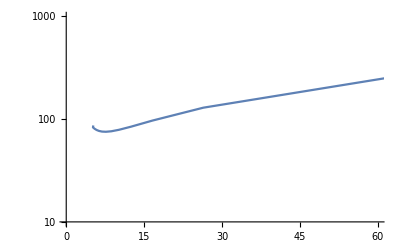

```mathematica
ListLogPlot[{{196.76400948798255,5571.418275343729},{195.53744363582396,2669.5710793031},{195.42087540662808,2068.503805578548},{168.82954476597547,813.5385044755983},{122.43294977161695,575.4532216194092},{125.21143909037812,513.283485837545},{105.85154543812992,434.84064074137257},{77.85717083916761,359.29794269749846},{98.4832414093555,352.820417007398},{74.03430278707798,317.98623915212727},{26.402315394848152,129.37372911063437},{16.614265967432427,96.94279559304691},{12.488049940425872,84.54150522536784},{10.144235422741598,78.79331446470903},{8.668640267941047,76.22029811518237},{7.644567363427574,75.41642251388127},{6.8888089842023055,75.73306011903956},{6.310552692868189,76.83602266540338},{5.847257793706908,78.51337566459549},{5.469691352155798,80.6511977721334},{5.152147568114839,83.16090519193497},{5.217013934544665,86.86007423579663}},PlotRange->{{0,60},{10,1000}},Joined->True]
```

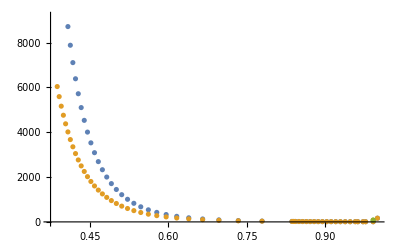

```mathematica
ListPlot[{Dat2,Dat3},PlotRange->{{0.953,1},{70,150}}]
```

```mathematica
di2={};
di3={};
Do[AppendTo[di2,{i,i2[i]}];
AppendTo[di3,{i,i3[i]}],
{i,0.95405,0.9984759995489378,0.001}]
```

```mathematica
di22={};
di32={};
Do[AppendTo[di22,{i,i22[i]}];
AppendTo[di32,{i,i32[i]}],
{i,0.9998464261591169,1,0.0001}]
```

```mathematica
di2=Join[di2,di22];
di3=Join[di3,di32];
```

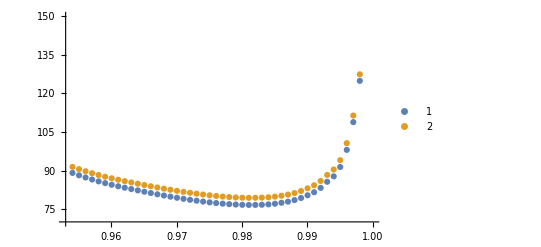

```mathematica
ListPlot[{di2,di3},PlotLegends->Automatic,PlotRange->{{0.953,1},{70,150}}]
```

```mathematica
Export["w_Num_H_P.dat",di2]
Export["w_Ene_H_P.dat",di3]
(*Export["Num_Ene_H_N.dat",Dat1]*)
```

w_Num_H_P.dat

w_Ene_H_P.dat

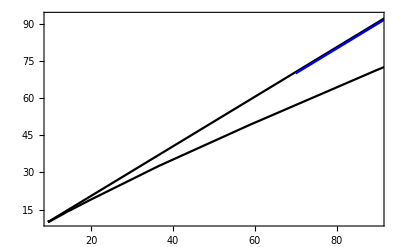

```mathematica
ListPlot[{Dat1,dat},PlotRange->{{10,90},{10,93}},PlotTheme->"Scientific",PlotStyle->{Black,Blue},Joined->True]
```

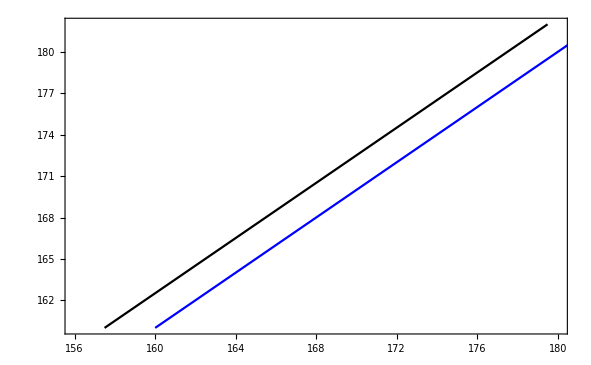

```mathematica
ListPlot[{Dat1,dat},PlotRange->{{156,180},{160,182}},PlotTheme->"Scientific",PlotStyle->{Black,Blue},Joined->True]
```

```mathematica
Dat2N={{0.9999995207157898,165.07899837645974},{0.9918107720880629,7.42050448913508},{0.9773564575675739,7.011618741661745},{0.9723871014804728,6.908868647886387},(*{0.9624652220917436,7.90537653525719},{0.9575473875684575,9.556124540769522},*){0.9478481489709842,7.8912000422521515},{0.9383659516701663,8.513884113554747},{0.9291239932949891,9.074042616766299},{0.9201313108001683,9.766523453420863},{0.9113897089244307,10.46592331575123},{0.9028971062183845,11.23650561987072},{0.8946481144672654,12.054462953730335},{0.8866353439752958,12.92227602354538},{0.878852101130706,14.342610167356652},(*{0.8712895259625596,14.805282340665238},*){0.8639400693060306,15.822392853416078},{0.8567948948772361,16.891564575598576},{0.8498465804823888,18.013215639612277},{0.8430871226575917,19.236590065526276},{0.8397756686359639,19.797446897564832},{0.8365083431232883,20.419870345382698},{0.7792281406244599,36.488103660654716},{0.7338129340118398,58.67205427614446},{0.696688024813614,89.5579295988949},{0.6655979441170108,130.5281061255086},{0.6390553518425344,182.72645701069885},{0.6160385486514806,248.00762458146767},{0.5958204645637497,328.022727362784},{0.5778682884855366,424.41548427655925},{0.5617811490863667,538.9443212873239},{0.5472513804946141,673.355939952848},{0.5340384133417744,829.4814543177444},{0.5219506559272629,1009.1621036072661},{0.5108335204507295,1214.2799639220511},{0.5005611251183273,1446.8392822431742},{0.4910292284122836,1708.5238229722356},{0.4821508284497754,2001.5578451122963},{0.4738526759966446,2327.8826748386605},{0.4660726898167017,2689.5261079825345},{0.45875779679090745,3088.551831585773},{0.4518622255255901,3527.0511723376},{0.44534626650868525,4007.1426022233236},{0.4391754793410385,4530.969553145172},{0.4333195263659412,5100.716960278185},{0.42775183524014715,5718.527521918772},{0.4224487319929132,6386.671316602502},{0.41738942075742513,7107.37133399132},{0.41255518759458343,7882.89217353028},{0.4079293352782265,8715.519937664765},{0.40349678011570467,9607.565314999048},{0.3992441870875326,10561.353033508274},{0.3951591624249573,11579.239485919734},{0.3912307662288609,12663.5980010018},{0.38744884712284566,13816.817214595721}};

Dat3N={{0.9999995207157898,165.62878558085168},{0.9918107720880629,7.995048875339242},{0.9773564575675739,7.595528467457925},{0.9723871014804728,7.48627201756194},(*{0.9624652220917436,8.49351202772372},{0.9575473875684575,10.193337182999235},*){0.9478481489709842,8.423493533310975},{0.9383659516701663,9.01745921020467},{0.9291239932949891,9.533356483645779},{0.9201313108001683,10.17668761947927},{0.9113897089244307,10.813610921942137},{0.9028971062183845,11.512649118214862},{0.8946481144672654,12.247649986848833},{0.8866353439752958,13.020518781375802},{0.878852101130706,14.393159361679752},(*{0.8712895259625596,14.675187223215687},*){0.8639400693060306,15.557599429550143},{0.8567948948772361,16.47743374310312},{0.8498465804823888,17.434527108148295},{0.8430871226575917,18.48495470445745},{0.8397756686359639,18.941882021087668},{0.8365083431232883,19.46351595117748},{0.7792281406244599,32.59387423479514},{0.7338129340118398,49.14755639824447},{0.696688024813614,71.14979574997808},{0.6655979441170108,99.10932009596155},{0.6390553518425344,133.0532349612975},{0.6160385486514806,173.94161369075937},{0.5958204645637497,222.38336695314095},{0.5778682884855366,278.90148797185276},{0.5617811490863667,344.12878685797386},{0.5472513804946141,418.61333918914096},{0.5340384133417744,502.9811658136336},{0.5219506559272629,597.8115623881891},{0.5108335204507295,703.6925759298606},{0.5005611251183273,821.3824214965507},{0.4910292284122836,950.9715362305316},{0.4821508284497754,1093.5081644591623},{0.4738526759966446,1249.453226397304},{0.4660726898167017,1419.37375546806},{0.45875779679090745,1603.8512943120224},{0.4518622255255901,1803.466627032461},{0.44534626650868525,2018.8003742192695},{0.4391754793410385,2250.4321789878704},{0.4333195263659412,2498.9744406869445},{0.42775183524014715,2764.8968189277603},{0.4224487319929132,3048.888076453383},{0.41738942075742513,3351.486664410746},{0.41255518759458343,3673.270414423965},{0.4079293352782265,4014.8133723767874},{0.40349678011570467,4376.694605606785},{0.3992441870875326,4759.478045259094},{0.3951591624249573,5163.74699903734},{0.3912307662288609,5590.077056704366},{0.38744884712284566,6039.034316431667}};

i2N=Interpolation[{{0.9918107720880629,7.42050448913508},{0.9773564575675739,7.011618741661745},{0.9723871014804728,6.908868647886387},(*{0.9624652220917436,7.90537653525719},{0.9575473875684575,9.556124540769522},*){0.9478481489709842,7.8912000422521515},{0.9383659516701663,8.513884113554747},{0.9291239932949891,9.074042616766299},{0.9201313108001683,9.766523453420863},{0.9113897089244307,10.46592331575123},{0.9028971062183845,11.23650561987072},{0.8946481144672654,12.054462953730335},{0.8866353439752958,12.92227602354538},(*{0.878852101130706,14.342610167356652},{0.8712895259625596,14.805282340665238},*){0.8639400693060306,15.822392853416078},{0.8567948948772361,16.891564575598576},{0.8498465804823888,18.013215639612277},{0.8430871226575917,19.236590065526276},{0.8397756686359639,19.797446897564832},{0.8365083431232883,20.419870345382698},{0.7792281406244599,36.488103660654716},{0.7338129340118398,58.67205427614446},{0.696688024813614,89.5579295988949},{0.6655979441170108,130.5281061255086},{0.6390553518425344,182.72645701069885},{0.6160385486514806,248.00762458146767},{0.5958204645637497,328.022727362784},{0.5778682884855366,424.41548427655925},{0.5617811490863667,538.9443212873239},{0.5472513804946141,673.355939952848},{0.5340384133417744,829.4814543177444},{0.5219506559272629,1009.1621036072661},{0.5108335204507295,1214.2799639220511},{0.5005611251183273,1446.8392822431742},{0.4910292284122836,1708.5238229722356},{0.4821508284497754,2001.5578451122963},{0.4738526759966446,2327.8826748386605},{0.4660726898167017,2689.5261079825345},{0.45875779679090745,3088.551831585773},{0.4518622255255901,3527.0511723376},{0.44534626650868525,4007.1426022233236},{0.4391754793410385,4530.969553145172},{0.4333195263659412,5100.716960278185},{0.42775183524014715,5718.527521918772},{0.4224487319929132,6386.671316602502},{0.41738942075742513,7107.37133399132},{0.41255518759458343,7882.89217353028},{0.4079293352782265,8715.519937664765},{0.40349678011570467,9607.565314999048},{0.3992441870875326,10561.353033508274},{0.3951591624249573,11579.239485919734},{0.3912307662288609,12663.5980010018},{0.38744884712284566,13816.817214595721}}]
i3N=Interpolation[{{0.9918107720880629,7.995048875339242},{0.9773564575675739,7.595528467457925},{0.9723871014804728,7.48627201756194},(*{0.9624652220917436,8.49351202772372},{0.9575473875684575,10.193337182999235},*){0.9478481489709842,8.423493533310975},{0.9383659516701663,9.01745921020467},{0.9291239932949891,9.533356483645779},{0.9201313108001683,10.17668761947927},{0.9113897089244307,10.813610921942137},{0.9028971062183845,11.512649118214862},{0.8946481144672654,12.247649986848833},(*{0.8866353439752958,13.020518781375802},{0.878852101130706,14.393159361679752},{0.8712895259625596,14.675187223215687},*){0.8639400693060306,15.557599429550143},{0.8567948948772361,16.47743374310312},{0.8498465804823888,17.434527108148295},{0.8430871226575917,18.48495470445745},{0.8397756686359639,18.941882021087668},{0.8365083431232883,19.46351595117748},{0.7792281406244599,32.59387423479514},{0.7338129340118398,49.14755639824447},{0.696688024813614,71.14979574997808},{0.6655979441170108,99.10932009596155},{0.6390553518425344,133.0532349612975},{0.6160385486514806,173.94161369075937},{0.5958204645637497,222.38336695314095},{0.5778682884855366,278.90148797185276},{0.5617811490863667,344.12878685797386},{0.5472513804946141,418.61333918914096},{0.5340384133417744,502.9811658136336},{0.5219506559272629,597.8115623881891},{0.5108335204507295,703.6925759298606},{0.5005611251183273,821.3824214965507},{0.4910292284122836,950.9715362305316},{0.4821508284497754,1093.5081644591623},{0.4738526759966446,1249.453226397304},{0.4660726898167017,1419.37375546806},{0.45875779679090745,1603.8512943120224},{0.4518622255255901,1803.466627032461},{0.44534626650868525,2018.8003742192695},{0.4391754793410385,2250.4321789878704},{0.4333195263659412,2498.9744406869445},{0.42775183524014715,2764.8968189277603},{0.4224487319929132,3048.888076453383},{0.41738942075742513,3351.486664410746},{0.41255518759458343,3673.270414423965},{0.4079293352782265,4014.8133723767874},{0.40349678011570467,4376.694605606785},{0.3992441870875326,4759.478045259094},{0.3951591624249573,5163.74699903734},{0.3912307662288609,5590.077056704366},{0.38744884712284566,6039.034316431667}}]

i22N=Interpolation[{{0.9999995207157898,165.07899837645974},{0.9918107720880629,7.42050448913508},{0.9773564575675739,7.011618741661745}},InterpolationOrder->1]
i32N=Interpolation[{{0.9999995207157898,165.62878558085168},{0.9918107720880629,7.995048875339242},{0.9773564575675739,7.595528467457925}},InterpolationOrder->1]
```

```mathematica
Dat2P={{0.99998046875,5862.371452807607},{0.9999775303335917,2807.7466515157193},{0.9999687150843667,2175.029576074262},{0.9999789995417958,853.9676381667914},{0.9999687150843667,603.3357656100748},{0.9999452077531001,537.8927682031199},{0.9999217004218335,455.3146467933877},{0.9998993352826282,375.78575601426087},{0.9998599936772586,368.9689959270112},{0.9998464261591169,332.2946782087112},{0.9984759995489378,133.65619190985578},{0.9962075834622321,99.43661705151068},{0.9932927009293323,86.3165217792886},{0.9898964354584507,80.2164844308349},{0.9861317754171623,77.47603682335294},{0.9820802824199164,76.61667954335589},{0.9778025103732645,76.95717982716245},{0.9733433353477622,78.14737006818855},{0.9687350122072801,79.9660269817315},{0.9639970167958337,82.2948710315314},{0.9591309602305742,85.04239498512412},{0.95405,89.06955979091487}}

Dat3P={{0.99998046875,5864.650816151294},{0.9999775303335917,2810.074820319053},{0.9999687150843667,2177.3724269247873},{0.9999789995417958,856.3563205006299},{0.9999687150843667,605.7402332835886},{0.9999452077531001,540.2984061447842},{0.9999217004218335,457.7269902540764},{0.9998993352826282,378.2083607342089},{0.9998599936772586,371.38991263936634},{0.9998464261591169,334.7223570022392},{0.9984759995489378,136.18287274803617},{0.9962075834622321,102.04504799268096},{0.9932927009293323,88.99105813196616},{0.9898964354584507,82.9403310154832},{0.9861317754171623,80.23189275282355},{0.9820802824199164,79.38570790934871},{0.9778025103732645,79.7190106516206},{0.9733433353477622,80.88002385831935},{0.9687350122072801,82.64565859431104},{0.9639970167958337,84.89599765487726},{0.9591309602305742,87.53779493887892},{0.95405,91.43165709031224}}

i2P=Interpolation[{{0.9984759995489378,133.65619190985578},{0.9962075834622321,99.43661705151068},{0.9932927009293323,86.3165217792886},{0.9898964354584507,80.2164844308349},{0.9861317754171623,77.47603682335294},{0.9820802824199164,76.61667954335589},{0.9778025103732645,76.95717982716245},{0.9733433353477622,78.14737006818855},{0.9687350122072801,79.9660269817315},{0.9639970167958337,82.2948710315314},{0.9591309602305742,85.04239498512412},{0.95405,89.06955979091487}}]

i3P=Interpolation[{{0.9984759995489378,136.18287274803617},{0.9962075834622321,102.04504799268096},{0.9932927009293323,88.99105813196616},{0.9898964354584507,82.9403310154832},{0.9861317754171623,80.23189275282355},{0.9820802824199164,79.38570790934871},{0.9778025103732645,79.7190106516206},{0.9733433353477622,80.88002385831935},{0.9687350122072801,82.64565859431104},{0.9639970167958337,84.89599765487726},{0.9591309602305742,87.53779493887892},{0.95405,91.43165709031224}}]

i22P=Interpolation[{{0.99998046875,5862.371452807607},{0.9999775303335917,2807.7466515157193}(*,{0.9999687150843667,2175.029576074262}*),{0.9999789995417958,853.9676381667914},{0.9999687150843667,603.3357656100748},{0.9999452077531001,537.8927682031199},{0.9999217004218335,455.3146467933877},{0.9998993352826282,375.78575601426087},{0.9998599936772586,368.9689959270112},{0.9998464261591169,332.2946782087112},{0.9984759995489378,133.65619190985578}},InterpolationOrder->1]

i32P=Interpolation[{{0.99998046875,5864.650816151294},{0.9999775303335917,2810.074820319053}(*,{0.9999687150843667,2177.3724269247873}*),{0.9999789995417958,856.3563205006299},{0.9999687150843667,605.7402332835886},{0.9999452077531001,540.2984061447842},{0.9999217004218335,457.7269902540764},{0.9998993352826282,378.2083607342089},{0.9998599936772586,371.38991263936634},{0.9998464261591169,334.7223570022392},{0.9984759995489378,136.18287274803617}},InterpolationOrder->1]
```

#### BHorndeski

```mathematica
Quit[]
```

```mathematica
eqphi=-m^2 r^2 ϕ[r]+r (r w^2 ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((11+2 r^2 w^2) ϕ'[r]+22 r ϕ''[r])-4 ϕ'[r]^2 (10 r w^2 ϕ'[r]+(9+4 r^2 w^2) ϕ''[r]))==0;
```

```mathematica
seEq=(Series[eqphi[[1]],{r,0,8}]//Simplify)/.φ'[0]-> 0;
ord0=Coefficient[seEq,r,0];
ord1=Coefficient[seEq,r,1];
ord2=Coefficient[seEq,r,2];
ord3=Coefficient[seEq,r,3];
ord4=Coefficient[seEq,r,4];
ord5=Coefficient[seEq,r,5];
ord6=Coefficient[seEq,r,6];
ord7=Coefficient[seEq,r,7];
ord8=Coefficient[seEq,r,8];
```

```mathematica
eqPhi=Series[ϕ[r],{r,0,8}]/.φ'[0]-> 0//Normal;
eqdPhi=Series[ϕ'[r],{r,0,7}]/.φ'[0]-> 0//Normal;
```

```mathematica
(* one *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[1]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond1={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* two *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[2]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond2={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* three *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[3]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond3={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(*sigma=eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ;*)
```

```mathematica
ClearAll[w,mS,η,rMin,ϕ0]
```

```mathematica
SeidelEqsList={};
SeidelBCList1={};
SeidelBCList2={};
SeidelBCList3={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{eqphi}];
AppendTo[SeidelCoefFunctionsList,{φ}];

AppendTo[SeidelBCList1,cond1];
AppendTo[SeidelBCList2,cond2];
AppendTo[SeidelBCList3,cond3];

(*AppendTo[SeidelBCList,{φ[rMin]==ϕ0, φ'[rMin] == 0 }];*)
```

```mathematica
ini={SeidelBCList1, SeidelBCList2, SeidelBCList3};
```

```mathematica
datViableP={{1.,2.86,0.770125,12,0.001,3},(*{1.,2.84,0.7716365872185278,11.060999999999979,0.001,3},*)(*{1.,2.82,0.7730806347642878,10.060999999999996,0.001,3},*)(*{1.,2.8,0.7745851308119633,11.06099999999999,0.001,3},*){1.,2.78,0.7761135077492844,15.060999999999996,0.001,3},{1.,2.75,0.7783938415288926,15.060999999999993,0.001,3},(*{1.,2.72,0.7806964843749999,15.060999999999996,0.001,3},*){1.,2.7,0.7822449547376848,25.06100000000003,0.001,3},{1.,2.65,0.7861634957974358,20.06100000000003,0.001,3},{1.,2.6,0.7901528317678485,20.06100000000003,0.001,3},{1.,2.55,0.7942159830927848,20.061000000000014,0.001,3},{1.,2.5,0.7983558304429055,20.061000000000014,0.001,3},{1.,2.45,0.8025751978497895,20.061000000000014,0.001,3}(*,{1.,2.4,0.8068768902870114,20.06100000000003,1.,0.001,3}*),{1.,2.35,0.8112637252807617,20.061000000000057,0.001,3},{1.,2.3,0.815738507270813,20.06100000000003,0.001,3},{1.,2.25,0.8203041187143326,20.06100000000003,0.001,3},{1.,2.2,0.8249636300778389,20.061000000000014,0.001,3},{1.,2.15,0.8297198441228915,20.061000000000014,0.001,3},{1.,2.1,0.8345757556261,20.06100000000003,0.001,3},{1.,2.,0.8445988314188136,20.061000000000057,0.001,3},{1.,1.9,0.8550566563002961,20.061000000000014,0.001,3.},{1.,1.8,0.8659721308804422,20.06100000000003,0.001,3.},{1,1.7641566171439984,0.87,28.170000000001604,0.001,3},{1.,1.7,0.8773653287038905,20.061000000000043,0.001,3.},{1.,1.6,0.889251053382468,20.061000000000014,0.001,3.},{1.,1.5,0.9016344451904297,20.061000000000014,0.001,3},{1.,1.4,0.9145037841796875,20.061000000000043,0.001,3},{1.,1.3,0.9278173828125001,20.061000000000053,0.001,3},{1.,1.2,0.9414862060546874,20.061000000000014,0.001,3},{1.,1.1,0.9553353917598724,20.061000000000043,0.001,3.},{1.,1.,0.9690234375,20.06100000000003,0.001,3},{1.,0.9,0.9818496704101562,20.06100000000003,0.001,3.},{1.,0.8,0.993223876953125,20.061000000000053,0.001,3.},(*{1.,0.7,0.9980639648437499,20.061000000000053,0.001,3.},*)(*{1.,0.78,0.994796905517578,20.061000000000053,0.001,2.}, *){1.,0.76,0.9971564483642578,20.061000000000053,0.001,2.}, {1.,0.74,0.997864483642578,30.061000000000053,0.001,2.},{1.,0.7,0.99964483642578,100,0.001,2.}(*,{1.,0.6,0.9995159912109375,20.061000000000043,0.001,3.}*),{1,0.6825, 0.999990234375000000,200,0.001,3}(*{1,0.682,0.99999999999,200,0.001,3},*)};
```

```mathematica
datViableN={(*{-1,200,.1012759251998,30,0.01,2},*){-1,3.4,.41793856334,20,0.01,2},{-1.,3.3,0.42257696476282125,15.060999999999996,30.,0.001,2.},{-1.,3.2,0.42741868345609285,14.060999999999996,0.001,2.},{-1.,3.1,0.4324795011056545,14.060999999999996,0.001,2.},{-1.,3.,0.4377771197616428,14.060999999999996,0.001,2.},{-1.,2.8,0.44916370674928163,14.060999999999996,0.001,2.},{-1.,2.6,0.4617670716752323,14.060999999999996,0.001,2.},{-1.,2.4,0.47582866010220326,14.060999999999996,0.001,2.},{-1.,2.3,0.4835012036913516,16.060999999999996,0.001,2.},{-1.,2.2,0.4916637282838694,16.060999999999996,0.001,2.},{-1.,2.1,0.5003725343240428,16.060999999999993,0.001,2.},{-1.,2.,0.5096931835894678,16.060999999999996,0.001,2.},{-1.,1.9,0.5197030004926888,15.060999999999996,0.001,2.},{-1.,1.8,0.5304939359182985,15.060999999999996,0.001,2.},{-1.,1.7,0.5421761948466499,15.060999999999996,0.001,2.},{-1.,1.6,0.5548830819525595,15.060999999999993,0.001,2.},{-1,1.5, 0.568778026578377680,15,0.01,2},{-1.,1.4,0.5840631169311036,15.060999999999996,0.001,2.},{-1.,1.3,0.6009934845506101,15.060999999999996,0.001,2.},{-1.,1.2,0.619894290301,15.06099999999999,0.001,2.},{-1.,1.1,0.6411891648478545,15.060999999999993,0.001,2.},{-1.,1.,0.6654413468170933,15.060999999999993,0.001,2.},{-1.,0.9,0.693418571871145,15.060999999999996,0.001,2.},{-1.,0.8,0.7261983250296968,15.060999999999996,0.001,2.},{-1,0.75,"0.744851633056108100",15,0.01,2},{-1.,0.74,0.7487935716572761,13.060999999999993,0.001,2.},{-1.,0.73,0.7528113814447068,13.060999999999993,0.001,2.},{-1.,0.72,0.7569073493158587,13.060999999999993,0.001,2.},{-1.,0.71,0.7610840312149496,13.060999999999993,0.001,2.},{-1.,0.7,0.7653439830861977,13.060999999999996,0.001,2.},{-1.,0.69,0.769690164443961,13.060999999999996,0.001,2.},{-1.,0.68,0.774125400279217,13.060999999999996,0.001,2.},{-1.,0.67,0.7786527846297033,13.060999999999993,0.001,2.},{-1.,0.66,0.7832754115331583,13.060999999999996,0.001,2.},{-1.,0.65,0.7879966440740788,13.060999999999996,0.001,2.},{-1.,0.64,0.7928201143837219,13.060999999999996,0.001,2.},{-1.,0.63,0.7977491855465857,13.060999999999996,0.001,2.},{-1.,0.62,0.8027878932640666,13.060999999999996,0.001,2.},{-1.,0.61,0.807940407760942,13.060999999999993,0.001,2.},{-1.,0.5959478335634352,0.8153806268563724,20,0.001,2},{-1.,0.58,0.824121853877925,15.060999999999996,0.001,2.},{-1.,0.56,0.8355594207274031,15.060999999999996,0.001,2.},{-1.,0.54,0.8475642898925049,15.060999999999996,0.001,2.},{-1.,0.52,0.8601807891916667,15.060999999999996,0.001,2.},{-1.,0.5051081756979723,0.87,20.750000000000444,0.01,2},{-1.,0.49,0.8803566619724883,20.061000000000053,0.001,2.},{-1.,0.48,0.887440805415177,20.061000000000014,0.001,2.},{-1.,0.46,0.9021844880215562,20.061000000000014,0.001,2.},{-1.,0.44,0.9177340182101899,20.061000000000014,0.001,2.},{-1.,0.42,0.9341209267802149,20.061000000000014,0.001,2.},{-1.,0.4,0.9513371701748521,20.061000000000014,0.001,2.},{-1,0.385,0.964900484864190000,20,0.001,2},{-1.,0.38,0.96925773469264,20.06100000000003,0.001,2.},{-1.,0.37,0.978358703464759,20.061000000000053,0.001,2.},{-1.,0.36,0.9873308491984716,20.061000000000043,0.001,2.},{-1,0.35,0.995939259294331000,20,0.01,2}, {-1,0.3415,0.999999999878928000,200,0.01,2}};
```

```mathematica
datViableN={{-1.,1.2,0.619894290301,15.06099999999999,0.001,2.},{-1.,1.1,0.6411891648478545,15.060999999999993,0.001,2.},{-1.,1.,0.6654413468170933,15.060999999999993,0.001,2.},{-1.,0.9,0.693418571871145,15.060999999999996,0.001,2.},{-1.,0.8,0.7261983250296968,15.060999999999996,0.001,2.},{-1,0.75,"0.744851633056108100",15,0.01,2},{-1.,0.74,0.7487935716572761,13.060999999999993,0.001,2.},{-1.,0.73,0.7528113814447068,13.060999999999993,0.001,2.},{-1.,0.72,0.7569073493158587,13.060999999999993,0.001,2.},{-1.,0.71,0.7610840312149496,13.060999999999993,0.001,2.},{-1.,0.7,0.7653439830861977,13.060999999999996,0.001,2.},{-1.,0.69,0.769690164443961,13.060999999999996,0.001,2.},{-1.,0.68,0.774125400279217,13.060999999999996,0.001,2.},{-1.,0.67,0.7786527846297033,13.060999999999993,0.001,2.},{-1.,0.66,0.7832754115331583,13.060999999999996,0.001,2.},{-1.,0.65,0.7879966440740788,13.060999999999996,0.001,2.},{-1.,0.64,0.7928201143837219,13.060999999999996,0.001,2.},{-1.,0.63,0.7977491855465857,13.060999999999996,0.001,2.},{-1.,0.62,0.8027878932640666,13.060999999999996,0.001,2.},{-1.,0.61,0.807940407760942,13.060999999999993,0.001,2.},{-1.,0.5959478335634352,0.8153806268563724,20,0.001,2},{-1.,0.58,0.824121853877925,15.060999999999996,0.001,2.},{-1.,0.56,0.8355594207274031,15.060999999999996,0.001,2.},{-1.,0.54,0.8475642898925049,15.060999999999996,0.001,2.},{-1.,0.52,0.8601807891916667,15.060999999999996,0.001,2.},{-1.,0.5051081756979723,0.87,20.750000000000444,0.01,2},{-1.,0.49,0.8803566619724883,20.061000000000053,0.001,2.},{-1.,0.48,0.887440805415177,20.061000000000014,0.001,2.},{-1.,0.46,0.9021844880215562,20.061000000000014,0.001,2.},{-1.,0.44,0.9177340182101899,20.061000000000014,0.001,2.},{-1.,0.42,0.9341209267802149,20.061000000000014,0.001,2.},{-1.,0.4,0.9513371701748521,20.061000000000014,0.001,2.},{-1,0.385,0.964900484864190000,20,0.001,2},{-1.,0.38,0.96925773469264,20.06100000000003,0.001,2.},{-1.,0.37,0.978358703464759,20.061000000000053,0.001,2.},{-1.,0.36,0.9873308491984716,20.061000000000043,0.001,2.},{-1,0.35,0.995939259294331000,20,0.01,2}, {-1,0.3415,0.999999999878928000,200,0.01,2}};
```

```mathematica
L1=1; η=1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.9818496704101562; rMax=20; α=1;(* .26,1.012476348812271000 *)
s1=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];
```

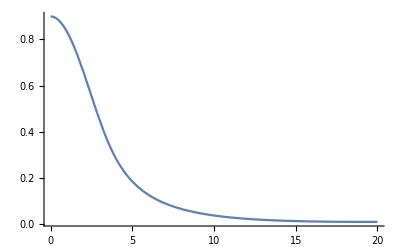

```mathematica
Plot[{Evaluate[φ[r]]/.s1},{r,rMin,rMax},PlotRange->All]
```

```mathematica
Table[
ClearAll[s, η, ϕ0, rMax, w];
AA=datViableP[[i]];
η=AA[[1]];
ϕ0=AA[[2]]; 
rMax=AA[[4]];
w=AA[[3]];
α=1;
mS=1;
rMin=AA[[5]];

s=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s]},
PlotRange->All,AxesOrigin->{0,0},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[datViableP]}](*Length[datViableN]*)
```

```mathematica
j0BH[r_]:=α (2 w ϕ[r]^2-(4 w η (-r^2 ϕ'[r]^4+r ϕ[r] ϕ'[r]^2 (-6 ϕ'[r]+r ϕ''[r])+3 r w^2 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+ϕ[r]^2 ϕ'[r] ((4+r^2 w^2) ϕ'[r]+8 r ϕ''[r])))/r^2);
 enerBH[r_]:=(m^2+w^2) ϕ[r]^2+ϕ'[r]^2-(8 η (r w^2 ϕ[r] ϕ'[r]^2 (-ϕ'[r]+r ϕ''[r])+ϕ'[r]^3 (ϕ'[r]+r ϕ''[r])+r w^4 ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])+w^2 ϕ[r]^2 ϕ'[r] (ϕ'[r]+2 r ϕ''[r])))/r^2;
```

```mathematica
Dat1={};
Dat2={};
Dat3={};
L1=1; mS=1; α=1;

Do[
Print[i];
ClearAll[s1, η, ϕ0, rMax, w];
AA=datViableN[[i]];
rMin=AA[[5]];
η=AA[[1]];
ϕ0=AA[[2]]; 
rMax=AA[[4]];
w=AA[[3]];

s1=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Ee=Last@NIntegrate[(Evaluate[enerBH[rB]/.s1])rB^2 Sin[θ],{rB,rMin,rMax},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"(*MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}*)];

Num=Last@NIntegrate[(Evaluate[j0BH[rB]/.s1])rB^2 Sin[θ],{rB,rMin,rMax},{θ,0,π},{ϕ,0,2π},Method->"LocalAdaptive"(*MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}*)];

AppendTo[Dat1,{Num,Ee}]; (*salvando datos para graficar *)
AppendTo[Dat2,{w,Num}]; (*salvando datos para graficar *)
AppendTo[Dat3,{w,Ee}]; (*salvando datos para graficar *)

,{i,1,Length[datViableN]}]
```

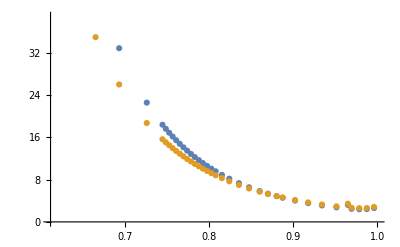

```mathematica
ListPlot[{Dat2,Dat3}]
```

```mathematica
di2={};
di3={};
Do[AppendTo[di2,{i,i2[i]}];
AppendTo[di3,{i,i3[i]}],
{i,0.770125,0.9971564483642578,0.001}]
```

```mathematica
di22={};
di32={};
Do[AppendTo[di22,{i,i22[i]}];
AppendTo[di32,{i,i32[i]}],
{i,0.998,1,0.0001}]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
di2=Join[di2,di22];
di3=Join[di3,di32];
```

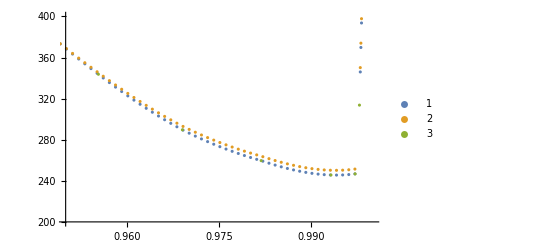

```mathematica
ListPlot[{di2,di3,Dat2},PlotLegends->Automatic,PlotRange->{{0.95,1},{200,400}}]
```

```mathematica
Export["w_Num_BH_P.dat",di2]
Export["w_Ene_BH_P.dat",di3]
(*Export["Num_Ene_BH_N.dat",Dat1]*)
```

```mathematica
Export["Num_Ene_BH_N.dat",Dat1]
```

Num_Ene_BH_N.dat

```mathematica
Export["w_Num2_BH_P.dat",dat4]
```

w_Num2_BH_P.dat

```mathematica
Export["w_Ene2_BH_P.dat",dat4]
```

w_Ene2_BH_P.dat

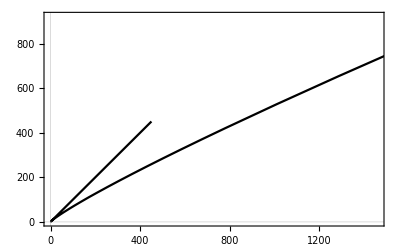

```mathematica
ListPlot[{Dat1},PlotTheme->"Scientific",PlotStyle->{Black,Blue},Joined->True]
```

```mathematica
dat={};
Do[AppendTo[dat,{i,i}],{i,70,1000}]
```

```mathematica
(*Datos Negativos *)
dat2N={{0.619894290301,82.65383786668882},{0.6411891648478545,62.480381730291754},{0.6654413468170933,46.0146393756051},{0.693418571871145,32.84003912218984},{0.7261983250296968,22.551819396478958},{0.7448516330561081,18.367097301474605},(*{0.7487935716572761,17.600831174015184},*){0.7528113814447068,16.857150978971713},(*{0.7569073493158587,16.135735520139683},*){0.7610840312149496,15.436242974156245},(*{0.7653439830861977,14.758281408602915},*){0.769690164443961,14.101478751042375},(*{0.774125400279217,13.465469466891486},*){0.7786527846297033,12.849902832668617},(*{0.7832754115331583,12.254419907116594},*){0.7879966440740788,11.6786619767266},(*{0.7928201143837219,11.12220883874118},*){0.7977491855465857,10.584799717519195},(*{0.8027878932640666,10.06600689149149},*){0.807940407760942,9.565439877709569},{0.8153806268563724,8.892500876905203},{0.824121853877925,8.170187380578811},{0.8355594207274031,7.3252015175239045},{0.8475642898925049,6.545337733576134},{0.8601807891916667,5.828035809785042},{0.87,5.333793725225562},{0.8803566619724883,4.864448322418198},{0.887440805415177,4.5722212108813585},{0.9021844880215562,4.030089505044522},{0.9177340182101899,3.54395553298377},{0.9341209267802149,3.115150366049511},{0.9513371701748521,2.7501108734840165}(*,{0.96490048486419`17.98448252463606,3.212914391692039}*),{0.96925773469264,2.47393132855617},{0.978358703464759,2.3934271585339806},{0.9873308491984716,2.4245280226371153},{0.995939259294331`17.998232852321593,2.625153735802054},{0.999999999878928`18.,450.9316371958784}};

dat3N={{0.619894290301,58.3794442290909},{0.6411891648478545,45.670636513000495},{0.6654413468170933,34.92490254835471},{0.693418571871145,25.985477874944873},{0.7261983250296968,18.69483958214322},{0.7448516330561081,15.618508540551565},(*{0.7487935716572761,15.046143022057668},*){0.7528113814447068,14.487798130664515},(*{0.7569073493158587,13.94324291948821},*){0.7610840312149496,13.41234334349009},(*{0.7653439830861977,12.894926317406886},*){0.769690164443961,12.390831919406017},(*{0.774125400279217,11.89990520502413},*){0.7786527846297033,11.421998781854823},(*{0.7832754115331583,10.956958530953939},*){0.7879966440740788,10.50463445812445},(*{0.7928201143837219,10.064821572657216},*){0.7977491855465857,9.637441579251503},(*{0.8027878932640666,9.222281089651712},*){0.807940407760942,8.81915432937707},{0.8153806268563724,8.273043377404427},{0.824121853877925,7.680926636582099},{0.8355594207274031,6.9798251529527855},{0.8475642898925049,6.323623259162794},{0.8601807891916667,5.711241267765607},{0.87,5.283900473910817},{0.8803566619724883,4.873009458643046},{0.887440805415177,4.614723266945306},{0.9021844880215562,4.129721371564621},{0.9177340182101899,3.6874654498538293},{0.9341209267802149,3.29053383123353},{0.9513371701748521,2.946525732841082}(*,{0.96490048486419`17.98448252463606,3.4396114624478544}*),{0.96925773469264,2.681490941919347},{0.978358703464759,2.6031432400786954},{0.9873308491984716,2.6337333577471775},{0.995939259294331`17.998232852321593,2.8333640440248726},{0.999999999878928`18.,451.1267826171462}};

i2N=Interpolation[{{0.619894290301,82.65383786668882},{0.6411891648478545,62.480381730291754},{0.6654413468170933,46.0146393756051},{0.693418571871145,32.84003912218984},{0.7261983250296968,22.551819396478958},{0.7448516330561081,18.367097301474605},(*{0.7487935716572761,17.600831174015184},*){0.7528113814447068,16.857150978971713},(*{0.7569073493158587,16.135735520139683},*){0.7610840312149496,15.436242974156245},(*{0.7653439830861977,14.758281408602915},*){0.769690164443961,14.101478751042375},(*{0.774125400279217,13.465469466891486},*){0.7786527846297033,12.849902832668617},(*{0.7832754115331583,12.254419907116594},*){0.7879966440740788,11.6786619767266},(*{0.7928201143837219,11.12220883874118},*){0.7977491855465857,10.584799717519195},(*{0.8027878932640666,10.06600689149149},*){0.807940407760942,9.565439877709569},{0.8153806268563724,8.892500876905203},{0.824121853877925,8.170187380578811},{0.8355594207274031,7.3252015175239045},{0.8475642898925049,6.545337733576134},{0.8601807891916667,5.828035809785042},{0.87,5.333793725225562},{0.8803566619724883,4.864448322418198},{0.887440805415177,4.5722212108813585},{0.9021844880215562,4.030089505044522},{0.9177340182101899,3.54395553298377},{0.9341209267802149,3.115150366049511},{0.9513371701748521,2.7501108734840165}(*,{0.96490048486419`17.98448252463606,3.212914391692039}*),{0.96925773469264,2.47393132855617},{0.978358703464759,2.3934271585339806},{0.9873308491984716,2.4245280226371153},{0.995939259294331`17.998232852321593,2.625153735802054}}];

i3N=Interpolation[{{0.619894290301,58.3794442290909},{0.6411891648478545,45.670636513000495},{0.6654413468170933,34.92490254835471},{0.693418571871145,25.985477874944873},{0.7261983250296968,18.69483958214322},{0.7448516330561081,15.618508540551565},(*{0.7487935716572761,15.046143022057668},*){0.7528113814447068,14.487798130664515},(*{0.7569073493158587,13.94324291948821},*){0.7610840312149496,13.41234334349009},(*{0.7653439830861977,12.894926317406886},*){0.769690164443961,12.390831919406017},(*{0.774125400279217,11.89990520502413},*){0.7786527846297033,11.421998781854823},(*{0.7832754115331583,10.956958530953939},*){0.7879966440740788,10.50463445812445},(*{0.7928201143837219,10.064821572657216},*){0.7977491855465857,9.637441579251503},(*{0.8027878932640666,9.222281089651712},*){0.807940407760942,8.81915432937707},{0.8153806268563724,8.273043377404427},{0.824121853877925,7.680926636582099},{0.8355594207274031,6.9798251529527855},{0.8475642898925049,6.323623259162794},{0.8601807891916667,5.711241267765607},{0.87,5.283900473910817},{0.8803566619724883,4.873009458643046},{0.887440805415177,4.614723266945306},{0.9021844880215562,4.129721371564621},{0.9177340182101899,3.6874654498538293},{0.9341209267802149,3.29053383123353},{0.9513371701748521,2.946525732841082}(*,{0.96490048486419`17.98448252463606,3.4396114624478544}*),{0.96925773469264,2.681490941919347},{0.978358703464759,2.6031432400786954},{0.9873308491984716,2.6337333577471775},{0.995939259294331`17.998232852321593,2.8333640440248726}}];

i22N=Interpolation[{{0.983894290301,2.3949889055522715},{0.984894290301,2.4010598544126194},{0.985894290301,2.409154911031118},{0.986894290301,2.419374650559152},{0.987894290301,2.4318196481481036},{0.988894290301,2.446590478949356},{0.989894290301,2.463787718114294},{0.990894290301,2.4835119407943003},{0.991894290301,2.505863722140758},{0.992894290301,2.5309436373050507},{0.993894290301,2.558852261438562},{0.994894290301,2.589690169692675},{0.995894290301,2.6235579372187736},{0.995939259294331`17.998232852321593,2.625153735802054},{0.999999999878928`18.,450.9316371958784}}]

i32N=Interpolation[{{0.983894290301,2.604564331142015},{0.984894290301,2.610542220111775},{0.985894290301,2.6185308145936976},{0.986894290301,2.628633595928103},{0.987894290301,2.6409540454553113},{0.988894290301,2.6555956445156417},{0.989894290301,2.672661874449415},{0.990894290301,2.6922562165969497},{0.991894290301,2.714482152298567},{0.992894290301,2.739443162894586},{0.993894290301,2.7672427297253273},{0.994894290301,2.7979843341311104},{0.995894290301,2.831771457452255},{0.995939259294331`17.998232852321593,2.8333640440248726},{0.999999999878928`18.,451.1267826171462}}]
```

```mathematica
Dat2P={{0.770125,4769.39211804879},{0.7761135077492844,4368.3404904019435},{0.7783938415288926,4224.530343435511},{0.7822449547376848,3992.49325738638},{0.7861634957974358,3769.744098048378},{0.7901528317678485,3556.0541675363656},{0.7942159830927848,3351.1949700508126},{0.7983558304429055,3154.943644349505},{0.8025751978497895,2967.0824655299434},{0.8112637252807617,2615.676497562116},{0.815738507270813,2451.711545693964},{0.8203041187143326,2295.296220649696},{0.8249636300778389,2146.2254472039126},{0.8297198441228915,2004.2981020628702},{0.8345757556261,1869.3144982027243},{0.8445988314188136,1619.3877069275622},{0.8550566563002961,1394.8881826172785},{0.8659721308804422,1194.2964052120617},{0.87,1127.9326335150122},{0.8773653287038905,1016.1289163164446},{0.889251053382468,858.9561157710128},{0.9016344451904297,721.3995853092819},{0.9145037841796875,602.1549501471208},{0.9278173828125001,500.07949176493554},{0.9414862060546874,414.1378570976407},{0.9553353917598724,343.7290196826426},{0.9690234375,289.6651544065789},{0.9818496704101562,259.6508430622028},{0.993223876953125,245.65433170963024},{0.9971564483642578,246.74597121831928},{0.997864483642578,313.6806623387588},{0.99964483642578,738.0250976743978},{0.999990234375`17.999995758822244,2187.511732622972}}
Dat3P={{0.770125,3997.056011567568},{0.7761135077492844,3687.0248346428084},{0.7783938415288926,3575.2498358355047},{0.7822449547376848,3394.1899721143222},{0.7861634957974358,3219.5134130911547},{0.7901528317678485,3051.096218636095},{0.7942159830927848,2888.814237764948},{0.7983558304429055,2732.5462818811743},{0.8025751978497895,2582.1740412866816},{0.8112637252807617,2298.650780021622},{0.815738507270813,2165.269178592204},{0.8203041187143326,2037.3221815590553},{0.8249636300778389,1914.695440885178},{0.8297198441228915,1797.2769910088327},{0.8345757556261,1684.9546607254345},{0.8445988314188136,1475.1500017587625},{0.8550566563002961,1284.3939171862137},{0.8659721308804422,1111.8106910483916},{0.87,1054.2091599317268},{0.8773653287038905,956.5355048958708},{0.889251053382468,817.7300505595357},{0.9016344451904297,694.581308159188},{0.9145037841796875,586.3226216499532},{0.9278173828125001,492.31676981931616},{0.9414862060546874,412.0112883290936},{0.9553353917598724,345.25398167784334},{0.9690234375,293.24841619694956},{0.9818496704101562,264.00584767936687},{0.993223876953125,250.2657844486127},{0.9971564483642578,251.4500010818025},{0.997864483642578,317.91769609622276},{0.99964483642578,741.9052864221088},{0.999990234375`17.999995758822244,2191.2898182232457}}

i2P=Interpolation[{{0.770125,4769.39211804879},{0.7761135077492844,4368.3404904019435},{0.7783938415288926,4224.530343435511},{0.7822449547376848,3992.49325738638},{0.7861634957974358,3769.744098048378},{0.7901528317678485,3556.0541675363656},{0.7942159830927848,3351.1949700508126},{0.7983558304429055,3154.943644349505},{0.8025751978497895,2967.0824655299434},{0.8112637252807617,2615.676497562116},{0.815738507270813,2451.711545693964},{0.8203041187143326,2295.296220649696},{0.8249636300778389,2146.2254472039126},{0.8297198441228915,2004.2981020628702},{0.8345757556261,1869.3144982027243},{0.8445988314188136,1619.3877069275622},{0.8550566563002961,1394.8881826172785},{0.8659721308804422,1194.2964052120617},{0.87,1127.9326335150122},{0.8773653287038905,1016.1289163164446},{0.889251053382468,858.9561157710128},{0.9016344451904297,721.3995853092819},{0.9145037841796875,602.1549501471208},{0.9278173828125001,500.07949176493554},{0.9414862060546874,414.1378570976407},{0.9553353917598724,343.7290196826426},{0.9690234375,289.6651544065789},{0.9818496704101562,259.6508430622028},{0.993223876953125,245.65433170963024},{0.9971564483642578,246.74597121831928}}]
i3P=Interpolation[{{0.770125,3997.056011567568},{0.7761135077492844,3687.0248346428084},{0.7783938415288926,3575.2498358355047},{0.7822449547376848,3394.1899721143222},{0.7861634957974358,3219.5134130911547},{0.7901528317678485,3051.096218636095},{0.7942159830927848,2888.814237764948},{0.7983558304429055,2732.5462818811743},{0.8025751978497895,2582.1740412866816},{0.8112637252807617,2298.650780021622},{0.815738507270813,2165.269178592204},{0.8203041187143326,2037.3221815590553},{0.8249636300778389,1914.695440885178},{0.8297198441228915,1797.2769910088327},{0.8345757556261,1684.9546607254345},{0.8445988314188136,1475.1500017587625},{0.8550566563002961,1284.3939171862137},{0.8659721308804422,1111.8106910483916},{0.87,1054.2091599317268},{0.8773653287038905,956.5355048958708},{0.889251053382468,817.7300505595357},{0.9016344451904297,694.581308159188},{0.9145037841796875,586.3226216499532},{0.9278173828125001,492.31676981931616},{0.9414862060546874,412.0112883290936},{0.9553353917598724,345.25398167784334},{0.9690234375,293.24841619694956},{0.9818496704101562,264.00584767936687},{0.993223876953125,250.2657844486127},{0.9971564483642578,251.4500010818025}}]

i22P=Interpolation[{{0.9818496704101562,259.6508430622028},{0.993223876953125,245.65433170963024},{0.9971564483642578,246.74597121831928},{0.997864483642578,313.6806623387588},{0.99964483642578,738.0250976743978},{0.999990234375`17.999995758822244,2187.511732622972}},InterpolationOrder->1]
i32P=Interpolation[{{0.9818496704101562,264.00584767936687},{0.993223876953125,250.2657844486127},{0.9971564483642578,251.4500010818025},{0.997864483642578,317.91769609622276},{0.99964483642578,741.9052864221088},{0.999990234375`17.999995758822244,2191.2898182232457}},InterpolationOrder->1]
```